```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/";
```

{{:0,:1,:2},{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

{{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

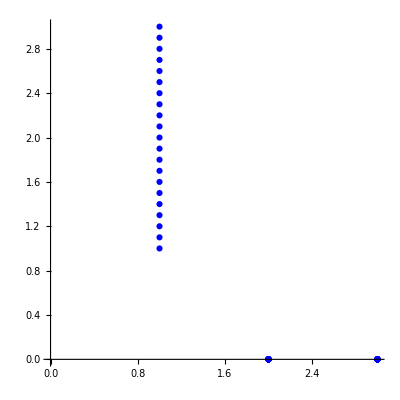

21

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabv=Table[Flatten[{{v[x],0,0}/.repv/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabv,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"v.csv",tabv]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/v.csv

```mathematica
(*write w from ODE to csv file*)
```

```mathematica
tabw=Table[{w[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"w.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/w.csv

```mathematica
(*write σ from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{0,3.,0,0},{0,2.9,0,0},{0,2.8,0,0},{0,2.7,0,0},{0,2.6,0,0},{0,2.5,0,0},{0,2.4,0,0},{0,2.3,0,0},{0,2.2,0,0},{0,2.1,0,0},{0,2.,0,0},{0,1.9,0,0},{0,1.8,0,0},{0,1.7,0,0},{0,1.6,0,0},{0,1.5,0,0},{0,1.4,0,0},{0,1.3,0,0},{0,1.2,0,0},{0,1.1,0,0},{0,1.,0,0}}

```mathematica
Export[outputdir<>"sigma.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/sigma.csv

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/psi.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{-0.514513,3.,0,0},{-0.520146,2.9,0,0},{-0.51479,2.8,0,0},{-0.498624,2.7,0,0},{-0.472184,2.6,0,0},{-0.436301,2.5,0,0},{-0.392032,2.4,0,0},{-0.34057,2.3,0,0},{-0.283164,2.2,0,0},{-0.22106,2.1,0,0},{-0.155451,2.,0,0},{-0.0874706,1.9,0,0},{-0.0181899,1.8,0,0},{0.051358,1.7,0,0},{0.120149,1.6,0,0},{0.187134,1.5,0,0},{0.251215,1.4,0,0},{0.311229,1.3,0,0},{0.365955,1.2,0,0},{0.414137,1.1,0,0},{0.454545,1.,0,0}}

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/mu.csv

```mathematica
(*write X from ODE to csv file*)
```

```mathematica
tabX=Table[Flatten[{{X1[x],X2[x],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabX,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"X.csv",tabX]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/flow/lagrangian_approach/one_dimension/solution_ode/X.csv